# RF Modulation Sweep (Frequency) - Photon Correlation Counts

## Last Updated: 04/21/2022

```mathematica
(*Quit[]*)
```

```mathematica
Remove["Global`*"];ClearInOut[];
```

## Parameters

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2023-05-09";
(*directoryString="C:\\Users\\EGGS2\\Documents\\datatmp_rf";*)
```

```mathematica
(*select runs*)
ridList={20545};
```

## Setup

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Evaluations

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[Power::infy];
Off[FindFit::nrjnum];
Off[Infinity::indet];
];
```

## Functions

### General

```mathematica
(*play sound when finished*)
Done[type_:"email",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],"none",EmitSound[soundDJ]
];
];
```

### Sided Conversion

```mathematica
(*convert double-sided to single-sided*)
GetSingleSidedX[data_List]:=If[OddQ[#2],#1[[;;(#2-1)/2]],#1[[;;(#2-2)/2]]]&[data,Length[data]];
```

```mathematica
GetSingleSidedY[data_List]:=With[
{trimmedData=If[OddQ[#2],#1[[;;(#2-1)/2]],#1[[;;(#2-2)/2]]]&[data,Length[data]]},
Return[(2*#1-UnitVector[#2,1]*#1[[1]])&[trimmedData,Length[trimmedData]]]
];
```

### Dataset Processing

```mathematica
(*import raw counts and demodulate*)
ProcessDatasetCounts[filename_]:=Module[
{
(*actual data*)
dataset,
datasetFrequencies=Import[filename,{"/datasets/xArr"}],
datasetCounts=Import[filename,{"/datasets/results"}],
correlatedSignal,correlatedAmplitude,correlatedPhase,
(*parameters*)
modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],
shimVoltage=Import[filename,{"/datasets/dc_channel_voltage"}],
(*processing*)
results
},

(*refine dataset*)
dataset=AssociationThread[datasetFrequencies->datasetCounts];
(*dataset=KeySort[dataset];*)

(*demodulate counts*)
correlatedSignal=KeyValueMap[
Total[Exp[ⅈ*(2*π*#1*1*^6)*#2]]/Length[#2]&,
dataset
];
{correlatedAmplitude,correlatedSignal}=Transpose[AbsArg[correlatedSignal]];

(*format data*)
results=Transpose[
{datasetFrequencies,ConstantArray[shimVoltage,Length[correlatedAmplitude]],##}&@@{correlatedAmplitude,correlatedSignal}
];

(*clean up mess*)
Remove[dataset,datasetFrequencies,datasetCounts];
ClearSystemCache[];
ClearInOut[];

(*return dataset*)
Return[results];
]
```

```mathematica
(*import already demodulated dataset*)
ProcessDataset[filename_]:=Module[
{
(*actual data*)
datasetRaw=Import[filename,{"/datasets/results"}],
(*parameters*)
(*modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],
shimVoltage=Import[filename,{"/datasets/dc_channel_voltage"}],*)
(*processing*)
results
},

(*refine dataset*)
(*dataset=KeySort[dataset];*)

(*format data*)
(*results=Transpose[
(datasetRaw[[;;,1]],ConstantArray[shimVoltage,Length[datasetRaw]],datasetRaw[[;;,3]],datasetRaw[[;;,4]]}
];*)
results=datasetRaw;

(*clean up mess*)
Remove[datasetRaw];
ClearSystemCache[];
ClearInOut[];

(*return dataset*)
Return[results];
]
```

## Import

## Import File

```mathematica
(*select file with give RID from all subdirectories*)
filenamesAll=FileNames["*.h5",directoryString,Infinity];
filenamesDJ=Select[filenamesAll,StringContainsQ[#,ToString/@ridList]&];
```

```mathematica
(*just select dataset of interest as the first one that shows up that matches our RID*)
filenameDJ=First@filenamesDJ;
```

## Extract Values

```mathematica
(*import and process data*)
dataset=ProcessDataset[filenameDJ];
(*sort dataset*)
dataset=SortBy[dataset,First];
```

```mathematica
(*get shim channel name*)
shimChannelName=Import[filenameDJ,{"/datasets/dc_channel_name"}];
```

```mathematica
(*get modulation parameters*)
modAttenuation=Import[filenameDJ,{"/datasets/modulation_attenuation_db"}];
numCounts=Import[filenameDJ,{"/datasets/num_counts"}];
```

## Plot

## 3D Summary Plots

```mathematica
(*signal density plot*)
amplitudeDensityPlot=ListDensityPlot[
dataset[[;;,;;3]],
PlotLegends->Automatic,
PlotRange->Full,
(*ColorFunction->,*)
ColorFunctionScaling->True,
FrameLabel->{ 
{Style[shimChannelName<>" Voltage (V)",{Black,Directive[15]}],None},
{Style["Secular Frequency (MHz)",{Black,Directive[15]}],Style["Signal Amplitude - RID: "<>ToString[ridList],{Black,Directive[15]}]}
}
];
```

```mathematica
(*phase density plot*)
phaseDensityPlot=ListDensityPlot[
dataset[[;;,{1,2,4}]],
PlotLegends->Automatic,
PlotRange->Full,
FrameLabel->{ 
{Style["V Shim"<>" Voltage (V)",{Black,Directive[15]}],None},
{Style["Secular Frequency (MHz)",{Black,Directive[15]}],Style["Signal Phase - RID: "<>ToString[ridList],{Black,Directive[15]}]}
}
];
```

## Individual Plots

### Format Data

```mathematica
(*separate data by shim voltage*)
individualPlotData=GroupBy[dataset,#[[2]]&,#[[;;,{1,3,4}]]&]//KeySort;
```

```mathematica
(*get min/max IV values for plotting later on*)
{indVar1Min,indVar1Max}={Min[#],Max[#]}&[individualPlotData[[1,;;,1]]];
```

### Create Base Plots

```mathematica
(*amplitude plots*)
amplitudePlots=ListLinePlot[
#[[;;,{1,2}]],
PlotRange->Full,
FrameLabel->{ 
{Style["Correlated Fraction",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Correlated Signal Amplitude - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
}
]&/@individualPlotData;
```

```mathematica
(*phase plots*)
phasePlots=ListLinePlot[
#[[;;,{1,3}]],
DataRange->dataset[[{1,-1},1]],
PlotRange->Full,
FrameLabel->{ 
{Style["Phase (rad.)",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Correlated Signal Phase - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
}
]&/@individualPlotData;
```

## Fit Data

### Fit Amplitude

```mathematica
(*get amplitude data*)
amplitudeData=#[[;;,{1,2}]]&/@individualPlotData;
```

```mathematica
(*create lorentz model for fitting*)
lorentzModel=α/(√((x^2-β^2)^2+(x*γ)^2));
lorentzConstraints={};
```

```mathematica
(*fit lorentz model!*)
AbsoluteTiming[
lorentzFits=ParallelMap[
FindFit[#,Join[{lorentzModel,lorentzConstraints}],{α,β,γ},x,MaxIterations->1000000]&,
amplitudeData
];
]
```

{0.0570158,Null}

```mathematica
(*get amplitude fit functions*)
amplitudeFunctions=(lorentzModel/.#)&/@lorentzFits;
fittedAmplitudePlots=Plot[
#,
{x,indVar1Min,indVar1Max},
PlotStyle->{Dashed,Orange},
PlotRange->Full
]&/@amplitudeFunctions;
```

```mathematica
(*plot raw data with fit line*)
amplitudeFinalPlots=MapThread[Show[#1,#2]&,Transpose[{amplitudePlots,fittedAmplitudePlots}]];
```

### Fit Phases

```mathematica
(*process phase data for fitting*)
rawPhaseData=#[[;;,{1,3}]]&/@individualPlotData;
processedPhaseData=Transpose[{#[[;;,1]],Tan[#[[;;,3]]]}]&/@individualPlotData;
(*plot processed phase data*)
processedPhasePlots=ListLinePlot[
#,
Joined->True
]&/@processedPhaseData;
```

```mathematica
(*create phase model*)
phaseModel=ArcTan[α*x/(x^2-β^2)+γ];
phaseConstraints={(*α>0,β>0,Abs[γ]<π/2*)};
(*fit phase & get fit functions*)
AbsoluteTiming[
phaseFits=ParallelMap[
FindFit[#,Join[{phaseModel,phaseConstraints}],{α,β,γ},x,MaxIterations->10000]&,
rawPhaseData
];
]
```

{0.303195,Null}

```mathematica
(*get phase fit functions*)
rawPhaseFunctions=(phaseModel/.#)&/@phaseFits;
processedPhaseFunctions=Tan[rawPhaseFunctions];
```

```mathematica
(*create fitted plots for visualization*)
fittedRawPhasePlots=Plot[
#,
{x,indVar1Min,indVar1Max},
PlotStyle->{Dashed,Orange}
]&/@rawPhaseFunctions;
fittedProcessedPhasePlots=Plot[
#,
{x,indVar1Min,indVar1Max},
PlotStyle->{Dashed,Orange}
]&/@processedPhaseFunctions;
```

```mathematica
(*plot fits with data*)
rawPhaseFinalPlots=MapThread[Show[#1,#2]&,Transpose[{phasePlots,fittedRawPhasePlots}]];
processedPhaseFinalPlots=MapThread[Show[#1,#2]&,Transpose[{processedPhasePlots,fittedProcessedPhasePlots}]];
```

```mathematica
{rawPhaseFinalPlots[[#]],processedPhaseFinalPlots[[#]]}&/@Range[Length[rawPhaseFinalPlots]];
```

### Extract Zero Crossings

```mathematica
(*fit resonances*)
AbsoluteTiming[
fittedResonances=ParallelMap[
x/.(FindRoot[#==0,{x,(indVar1Min+indVar1Max)/2}])&,
rawPhaseFunctions
];
]
(*format data for plotting*)
fittedResPlotData=Transpose[{Values[#],Keys[#]}&[fittedResonances]];
```

{0.0178498,Null}

```mathematica
(*plot resonances*)
resPlot=ListPlot[fittedResPlotData,Joined->True,PlotStyle->{Red,Dashed}];
```

## Summary

### Format Plot TMP

```mathematica
amplDataTMP=individualPlotData[[1,;;,{1,2}]];
maxAmpl=Max[amplDataTMP[[;;,2]]];
plotsTMP={
Plot[
amplitudeFunctions[[1]],
{x,indVar1Min,indVar1Max},
PlotStyle->{Dashed,Orange},
PlotRange->{0,1.1*maxAmpl}
],
ListLinePlot[
{
amplDataTMP,
amplDataTMP
},
PlotRange->Full,
FrameLabel->{ 
{Style["Correlated Fraction",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Correlated Signal Amplitude - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
},
PlotStyle->{{Automatic},{Dashed,Blue,Opacity[0.7]}},
Joined->{False,True}
],
ListPlot[
amplDataTMP,
PlotRange->Full,
FrameLabel->{ 
{Style["Correlated Fraction",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Correlated Signal Amplitude - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
}
]
};
```

### Format Plot TMP

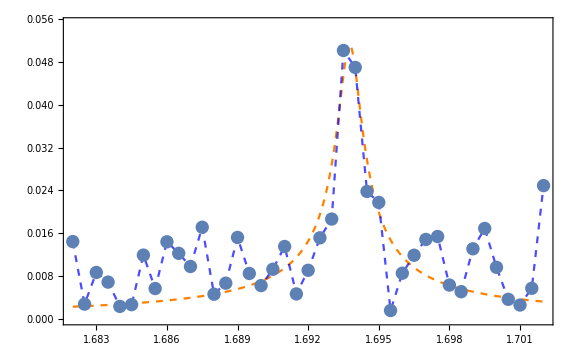

```mathematica
Show@@plotsTMP
```

```mathematica
(*plot raw data with fit line*)
amplitudeFinalPlots=MapThread[Show[#1,#2]&,Transpose[{amplitudePlots,fittedAmplitudePlots}]];
```

```mathematica
lorentzModel
```

α/(√((x^2-β^2)^2+x^2 γ^2))

```mathematica
lorentzFits[[1]]
```

{α→0.0000905699,β→1.69377,γ→-0.00104684}

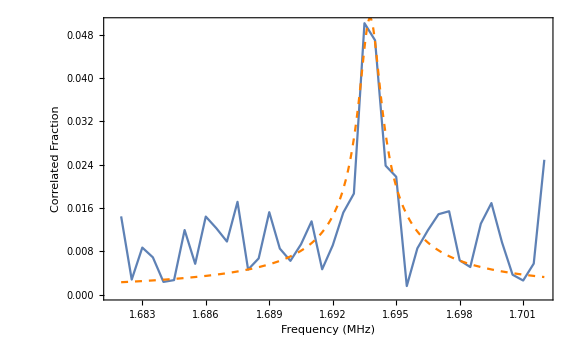

```mathematica
amplitudeFinalPlots[[1]]
```

```mathematica
amplitudeFinalPlots;
phasePlots;
```

Counts: 10000

Modulation Attenuation (dB): 10.

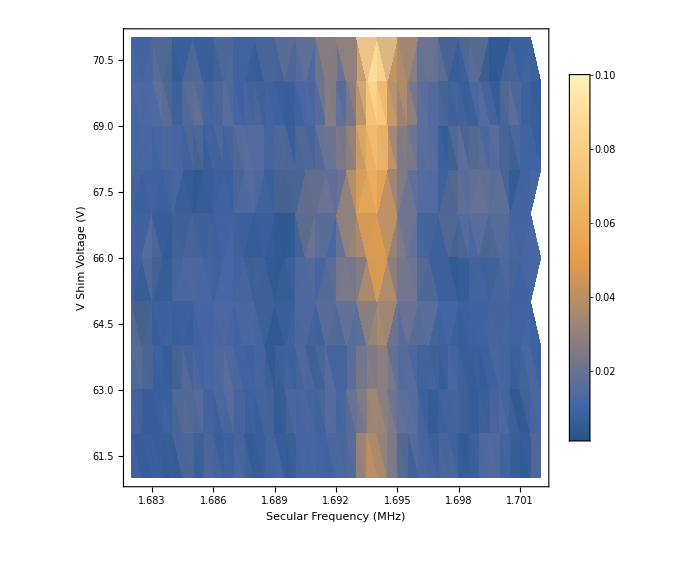
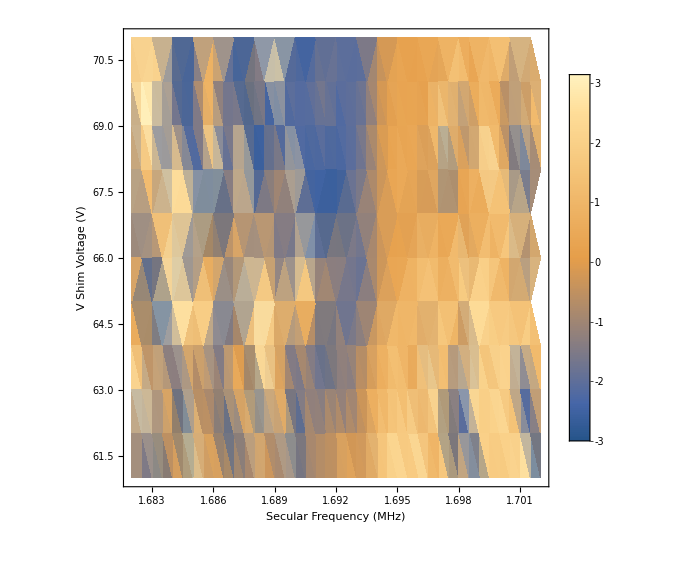
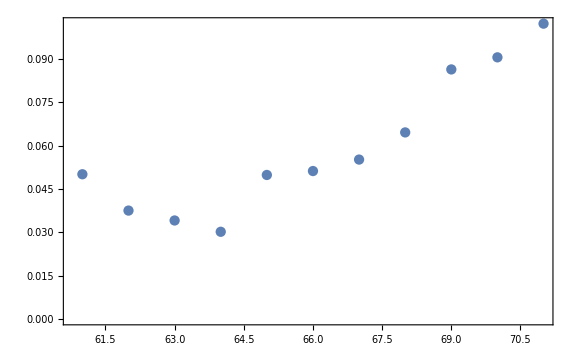

```mathematica
Print["Counts: "<>ToString[numCounts]];
Print["Modulation Attenuation (dB): "<>ToString[modAttenuation]];
{
Show[amplitudeDensityPlot(*,resPlot*)],
Show[phaseDensityPlot(*,resPlot*)],
ListPlot[Max[#[[;;,2]]]&/@amplitudeData]
}
```

## Deprecated

## Importing

```mathematica
(*(*get parameters*)
xArr=Import[#,{"/datasets/xArr"}]*1*^6&/@filenamesDJ;
xArr=Sort/@xArr;*)
```

## Processing

```mathematica
(*get time difference in seconds*)
(*datasets=(#[[;;,3]]-#[[;;,2]])/(1*^9)&/@datafile;*)
```

```mathematica
(*get total count times*)
(*datasetTimes=N[(#[[-1,3]]-#[[1,2]])/(1*^9)]&/@datafile;*)
(*get total count rates*)
(*datasetRates=numPoints/datasetTimes;*)
```

## Fitting

### Preprocess

```mathematica
(*fitData=histData;*)
```

```mathematica
(*(*remove offset*)
(*fitData=#-Mean[#]&/@fitData[[;;,;;,2]];*)*)
```

```mathematica
(*(*fit constraints*)
fitConstraints={
0<=a<=40,
1*2*π<=b<=2*π*3,
0<=c<=2π
};*)
```

### Fitting

```mathematica
(*(*fit sine*)
AbsoluteTiming[dataFits=ParallelMap[
NonlinearModelFit[#,
Join[{a*Sin[b*x+c]+d},fitConstraints],
{a,b,c,d},x,
Method->Automatic,
MaxIterations->1000
]&,
histData
];]*)
```

```mathematica
(*(*extract parameters*)
fittedParameterTables=#["ParameterTable"][[1]]&/@dataFits;
fittedParameters=fittedParameterTables[[;;,1,2;;5,{2,3}]];
{fittedAmplitudes,fittedFrequencies,fittedPhases,fittedOffsets}=Transpose[fittedParameters];*)
```

```mathematica
(*(*create step model*)
stepModel=α*HeavisideTheta[x-β]+γ;
stepConstraints={Abs[α]<=1.5*π,(*β>0,*)Abs[γ]<1.5*π};
(*fit phase & get fit functions*)
AbsoluteTiming[
stepFits=ParallelMap[
FindFit[#,Join[{stepModel,stepConstraints}],{α,β,γ},x,MaxIterations->1000]&,
rawPhaseData
];
]*)
```

### Plot Fit

```mathematica
(*fitSinFunc[A_,ω_,ϕ_,C_]:=A*Sin[ω*x+ϕ]+C;*)
```

```mathematica
(*(*create plot of fitted equation*)
fitSinEqns=fitSinFunc@@#&/@fittedParameters[[;;,;;,1]];
fitSinPlots=Plot[#,{x,histData[[1,1,1]],histData[[1,-1,1]]}]&/@fitSinEqns;*)
```

```mathematica
(*(*combine figures*)
combinedPlots=MapThread[Show[#1,#2]&,{histPlots,fitSinPlots}];*)
```

## Plotting

```mathematica
(*yz1=HistogramList[#,1000]&/@datasets;
mzdp1=Sqrt[GetSingleSidedY[Abs[Fourier[yz1[[1,2]]]]^2]];
ListLinePlot[%]*)
```